# Pigeonhole Principle

A simple counting argument with great power

## History

The Pigeonhole Principle is attributed to Peter Gustav Lejeune Dirichlet and its premise is of common sense. Nonetheless, this seemingly trivial revelation is a powerful tool in combinatorics as well as proving strong statements about collections without having to consider each element of a collection.

## Definition

Let n and k be positive integers, and let n > k. Suppose we have to place n identical balls into k identical boxes, where n > k. Then there will be at least one box in which we place at least two balls.

### Example:

#### Aside: Integer Partition

We will use the function IntegerPartitions to "distribute" the number of balls into the exact number of boxes, by partitioning the integer balls into exactly {boxes} parts. 

To give an example of an integer partition see that IntegerPartitions[4] yields a list of lists containing integers were the sum of those integers is 4.

```mathematica
IntegerPartitions[4]
```

{{4},{3,1},{2,2},{2,1,1},{1,1,1,1}}

The latter can be showed by applying the function Plus to each sublist that is returned by  IntegerPartitions[4].

```mathematica
Plus@@@IntegerPartitions[4]
```

{4,4,4,4,4}

Thus we see that an integer partition of the integer n into a list of length k is equivalent as distributing n balls into k boxes. Using the optional argument {k} we can specify that we want integer partitions of exactly k parts.

#### Applying the Pigeonhole Principle

Here we will see that if we try to distribute10 balls amongst 4 boxes, then there will at least be a box with at least 2 balls.

```mathematica
balls=10;
boxes=4;
```

Using IntegerPartition (as described above) we can find all the ways to distribute 10 balls amongst 4 boxes

```mathematica
distributions = IntegerPartitions[balls,{boxes}]
```

{{7,1,1,1},{6,2,1,1},{5,3,1,1},{5,2,2,1},{4,4,1,1},{4,3,2,1},{4,2,2,2},{3,3,3,1},{3,3,2,2}}

Visualize the distribution of balls in boxes with a BarChart

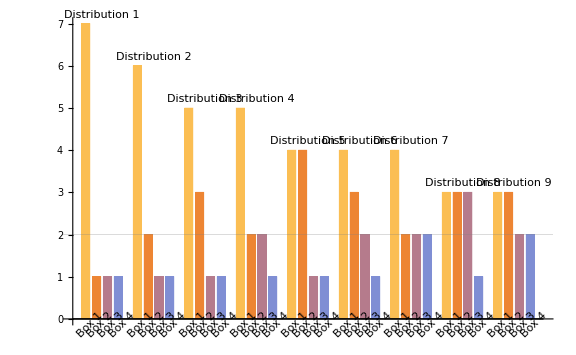

```mathematica
BarChart[
distributions, 
GridLines->{{},{2}}, (* make it easier to see boxes with at least 2 balls in them *)
ChartLabels->{
Placed[Table["Distribution " <> ToString[i], {i,Length@distributions}],Above],
(* enumerate the distribution possibilities *)Placed[Table["Box " <> ToString[i], {i,boxes}], Axis, Rotate[#, Pi/4]&]
(* enumerate the boxes of the distributions *)
},
ImageSize->Large
]
```

When n >> k such a bar chart will be unpractical to look at. Let us use AllTrue to show that the max value for each possible way to distribute the balls amongst boxes is in fact greater than or equal to 2!

```mathematica
AllTrue[IntegerPartitions[balls,{boxes}], Max[#] ≥  2&]
```

True

## Generalized Definition

Let n, m and r be positive integers so that n > r • m. Let us distribute n identical balls into m identical boxes. Then there will be at least one box in which we place at least r + 1 balls.

Using this generalization we can see that the first definition was the case where r = 1. r can be thought as the replicate threshold for how many balls each box will at least have.

Here we will see that if we try to distribute10 balls amongst three boxes with a replicate of 3, then there will at least be a box with at least 4 balls.

```mathematica
balls = 10;
boxes = 3;
replicates = 3;
```

As before we can enumerate all set of all ways to distribute the balls into boxes

```mathematica
distributions = IntegerPartitions[balls,{boxes}];
```

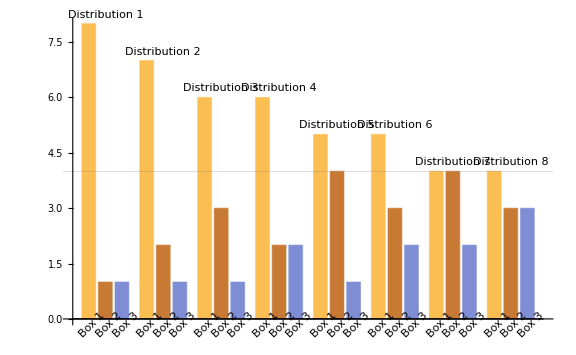

```mathematica
BarChart[
distributions, 
GridLines->{{},{replicates + 1}},(* highlight where r+1 is located at*)
ChartLabels->{
Placed[Table["Distribution " <> ToString[i], {i,Length@distributions}],Above],Placed[Table["Box " <> ToString[i], {i,boxes}], Axis, Rotate[#, Pi/4]&]
},
ImageSize->Large
]
```

When n >> rm such a bar chart will be unpractical to look at. Let us use AllTrue to show that the max value for each possible way to distribute the balls amongst boxes is in fact greater than or equal to replicates + 1!

```mathematica
AllTrue[IntegerPartitions[balls,{boxes}], Max[#] ≥  replicates + 1&]
```

True

## Examples

## Hair-raising power of the Pigeonhole Principle

Utilizing the Pigeonhole Principle we can prove that in New York City (NYC) there are at least two non-bald people with the same number of hair strands without having to hand count the strands on every individual’s head!

First let us identify the number of people living in NYC as well as the maximum number of hairs on the human head

```mathematica
population= LinguisticAssistant
hairs=Max[LinguisticAssistant]
```

8550405 people

150000

To show that at least two people in NYC have the same number of hair strands, we must confirm that there are at least 150,000 + 1 people in NYC who are not bald.

Using WolframAlpha we can figure out how many Americans have baldness

```mathematica
WolframAlpha["Baldness", "PodCells"][[3]]
WolframAlpha["Baldness",  {"Basic:DiseaseData","ComputableData"}][[1,2,2,-1]]
```

| male | female | all
fraction of US population | 1 in 1490 ≈ 0.067% | 1 in 1100 ≈ 0.091% | 1 in 1230 ≈ 0.081%
number of US patients | 119800 per year | 225600 per year | 345400 per year
average patient age | 41 years | 42 years | 42 years
diagnosis sample size | 26 visits | 52 visits | 78 visits
(estimates based on 131 748 patient visits to healthcare providers from NAMCS and NHAMCS, weighted for USA demographics, 2006 to 2007)

1 in 1230 ~~ 0.081%

```mathematica
baldness = 1/1230;
```

Thus we can calculate the number of non-bald people in NYC by using the pervasiveness of baldness and subtracting that percent from the populous.

```mathematica
baldPeople= Round[baldness * population]
notBaldPeople  = population - baldPeople
```

6952 people

8543453 people

As 8,543,453 is in fact greater than 150,000 it follows from the Pigeonhole Principle that there are at least two people with the same number of hair strands on their head.

## Geometric Insights to data

The examples so far shows how we can prove strong statements without enumeration or comparison of all objects under consideration. This concept can also be utilized for understanding the geometric relationship of data.

### Distance of Data Points

Lets assume we have a small dataset of with 10 points in ℝ^2 such that the range and domain are within the interval [0, 1] (i.e. within the unit square).

Generate ten random points within [0, 1]

```mathematica
data = RandomReal[1, {10,2}];
```

Utilizing the Pigeonhole Principle we can prove that at least two of our points are closer than 0.48.

To do so let us divide our unit square into 9 boxes of equal size (squares with side length of 1/3).

Plot our data with grid lines showing the boxes

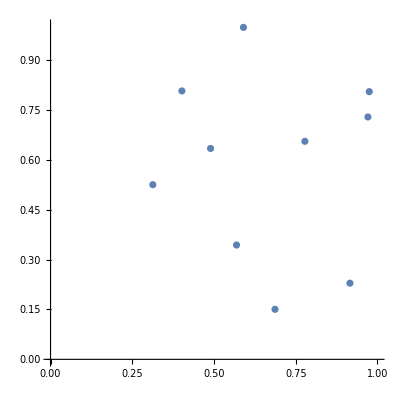

```mathematica
ListPlot[data, GridLines->{{1/3,2/3,3/3}, {1/3,2/3,3/3}}, PlotRange->{{0,1},{0,1}},AspectRatio->1]
```

Then following the Pigeonhole Principle at least one box will contain at least two points (as 10 > 9).

Since there will be two points in one box, the maximum distance those two points can obtain would be if each point were on opposite sides of the a diagonal of the box (i.e. the hypotenuse of the triangle made with the diagonal of the box).

We can calculate the hypotenuse using Pythagoras theorem as the sides of the triangle both have side length 1/3

```mathematica
hypotenuse = N@√(2(1/3)^2)
```

0.471405

Thus it follows that at least two points will be closer than 0.48!

We can also make a table of the distances between points and display in bold which points have a smaller distance than 0.48.

The pairwise distances between points can easily be calculated by using DistanceMatrix.
 Using a pattern we will display in bold which points have a smaller distance than 0.48.

```mathematica
TableForm[
ReplaceAll[DistanceMatrix[data],x_:>Style[x,Bold]/;(x<0.48∧x≠0.)],
TableHeadings->{Table["Point " <> ToString[i], {i,10}], Table["Point " <> ToString[i], {i,10}]}
]
```

| Point 1 | Point 2 | Point 3 | Point 4 | Point 5 | Point 6 | Point 7 | Point 8 | Point 9 | Point 10
Point 1 | 0. | 0.366787 | 0.842472 | 0.430556 | 0.425979 | 0.51424 | 0.332039 | 0.580173 | 0.687917 | 0.242841
Point 2 | 0.366787 | 0. | 1.04899 | 0.0830758 | 0.545211 | 0.661575 | 0.455158 | 0.869831 | 0.941515 | 0.455305
Point 3 | 0.842472 | 1.04899 | 0. | 1.05109 | 0.506947 | 0.391086 | 0.593921 | 0.338813 | 0.195679 | 0.61994
Point 4 | 0.430556 | 0.0830758 | 1.05109 | 0. | 0.544142 | 0.660274 | 0.462716 | 0.896961 | 0.957492 | 0.482213
Point 5 | 0.425979 | 0.545211 | 0.506947 | 0.544142 | 0. | 0.11654 | 0.100507 | 0.414725 | 0.431712 | 0.188396
Point 6 | 0.51424 | 0.661575 | 0.391086 | 0.660274 | 0.11654 | 0. | 0.210915 | 0.346056 | 0.332959 | 0.271545
Point 7 | 0.332039 | 0.455158 | 0.593921 | 0.462716 | 0.100507 | 0.210915 | 0. | 0.45214 | 0.496143 | 0.110897
Point 8 | 0.580173 | 0.869831 | 0.338813 | 0.896961 | 0.414725 | 0.346056 | 0.45214 | 0. | 0.143496 | 0.415416
Point 9 | 0.687917 | 0.941515 | 0.195679 | 0.957492 | 0.431712 | 0.332959 | 0.496143 | 0.143496 | 0. | 0.490111
Point 10 | 0.242841 | 0.455305 | 0.61994 | 0.482213 | 0.188396 | 0.271545 | 0.110897 | 0.415416 | 0.490111 | 0.

Thus knowing only the domain and range of our data we can already identify some properties thereof.

### Extension

We can further extend our insight to the spread of our data by changing r and m of the Pigeonhole Principle. For example, we can prove that with the same 10 data points that at least 3 of them are within a disk of radius 0.5.

To prove the above statement we will divide - along the diagonals - our unit square into four “boxes”. Doing so, and applying the Pigeonhole Principle - it is clear that at least one box will contain 3 points.

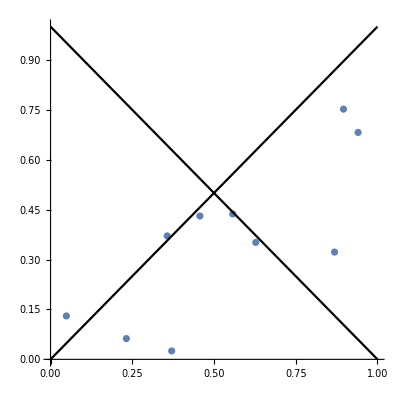

```mathematica
Show[
ListPlot[data, AspectRatio->1, PlotRange->{{0,1},{0,1}}],
ListLinePlot[{{{0,0},{1,1}},{{0,1},{1,0}}},PlotStyle->Black]
]
```

To prove that the three points within such a region falls within a disk with radius 0.5, we need to get the circumcircle of one of the triangles. In this case we will use the bottom triangle (defined by the points {{0,1},{0.5,0.5},{1,1}})

```mathematica
disk=Circumsphere[{{0,0},{0.5,0.5},{1,0}}]
```

Sphere[{0.5,0.},0.5]

Plotting the triangle and circumcircle together we can see their relationship.

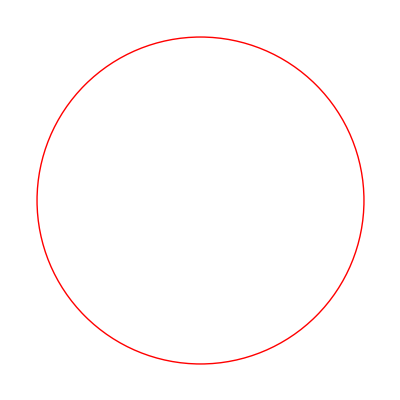

```mathematica
Show[
Graphics[{
Red,disk,
EdgeForm[Thick], Opacity[0],Triangle[{{0,0},{0.5,0.5},{1,0}}]
}]
]
```

To get the radius of the disk which can contain the triangle we need to get the distance from one point at the boundary to the center. We will use the bottom left corner of the triangle ({0,0}) as this point.

```mathematica
EuclideanDistance[RegionCentroid@disk, {0,0}]
```

0.5

Since at least three points will be in such a triangle, and the circumcircle around the triangle has a radius of 0.5 it follows that at least 3 points can be contained within a disk with radius 0.5.

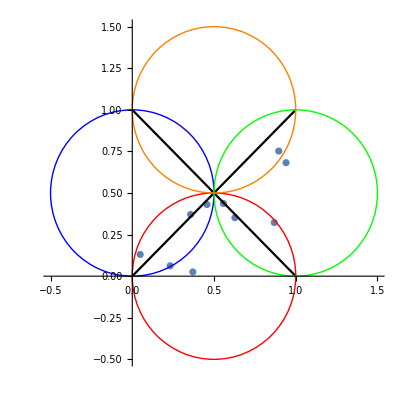

```mathematica
Show[
ListPlot[data, AspectRatio->1, PlotRange->{{-0.5,1.5},{-0.5,1.5}}],
ListLinePlot[{{{0,0},{1,1}},{{0,1},{1,0}}},PlotStyle->Black],
Graphics[{
Red,Circumsphere[{{0,0},{0.5,0.5},{1,0}}],
Blue,Circumsphere[{{0,0},{0.5,0.5},{0,1}}],
Green,Circumsphere[{{1,1},{0.5,0.5},{1,0}}],
Orange,Circumsphere[{{0,1},{0.5,0.5},{1,1}}],
Opacity[0], EdgeForm[Thick],Rectangle[{0,0},{1,1}],
}]
]
```

Alternatively one can see that the a disk with radius 0.5 fits centered in the unit square also dividing the unit square into four parts (excluding the region inside the disk).

```mathematica
Show[
Graphics[{
White,EdgeForm[Thick],Rectangle[{0,0},{1,1}],
Disk[{0.5,0.5},0.5]}]
]
```

-Graphics-

Assume the opposite (that three points are not within the disk above) then they must be within one of the four other regions. Again by the Pigeonhole Principle those 10 points must be within those four regions (and at least 3 are within one). 

Calculating the area, it is clear that the area of any one of these regions is much smaller than the area of the disk and the proof follows

```mathematica
rectA=Area[Rectangle[{0,0},{1,1}]]
diskA=Area[Disk[{0.5,0.5},0.5]]
```

1

0.785398

```mathematica
(rectA-diskA) / 4
```

0.0536505

Further Explorations

Fubini Principle

Authorship information

Sumner Magruder

June 20th 2016

Mag.ds@live.com